# Growth Index In F(R) Gravity.

## Enhancing/Dumping Gravitational Waves Using Viable F(R) Models Of Gravity

Hereafter, MP is the Planck mass, ms is a mass scale related to κ^2ρ0 with ρ0 being the current density of dust, χ is the current density of radiation over dust, M is a different Mass scale, each function/parameter ending with “dot” implies derivative with respect to cosmic time t hence it is rewritten appropriately as a derivative of redshift z, ρ is the sum of dust and radiation density, R0 is the real/proper Ricci scalar which is replaced in the f(R) function after calculations (for instance derivatives) have been carried, H2 stands for Hubble squared, it is easy to remember. YH is the function that we find as solution to the equations of motion instead of Hubble however yH is the proper statefinder we focus on, which is assigned the function satisfying the equations of motion, similar for the scalar field. Moreover, functions with the number 1 are similarly functions of the proper yH solution and facilitate us into extracting results for the statefinders. Referring to statefinders, q is as usual the deceleration parameter, j is the jerk and s is the snap, all of them connected with derivates of Hubble, however must be written with respect to redshift. Om is an extra statefinder for which mainly the current value matters, as it must coincide or actually be quite close to the current value of the matter density parameter Ωm. Finally, functions ending with DE are related to dark energy, meaning all the extra geometric terms appearing in the equations of motion. In particular, ωDE stands for the Equations of state (EoS) parameter whereas ΩDE  as before signifies the Dark Energy density parameter.

In this notebook we are mainly interested in the effective equation for state EoS of the universe, denotes as weff[z]. Expected value is near 0, ideally it should be below 1/3 in order to be accurate and rises towards such value. Moreover we focus also on aMdz parameter, the sign of which suggests enhancement or dumping of primordial gravitational waves. The present model is capable of yielding interesting results as the effective EoS resides near 0 for a while and afterwards starts increasing with a slow-rate converging on 1/3. Inserting an auxiliary mass scale here denotes as R00 manages also to produce a finite but quite large ratio between the first 2 derivatives of the f(R).

ΛCDM Values: Roughly speaking, q near -0.535, j near unity, snap near 0, Om near 0.315, ωDE near -1 (does not have to be exactly -1, it can also vary infinitesimally as shown in this particular model) and ΩDE near 0.685 such stat Om+ΩDE near unity (Friedman constraint). More details+accurate values can be found in arXiv: 1807.06209.

## 1. Designation Of Model.

### 1.1. Assigning Values To The Free Parameters.

Suppose we have a similar f(R) model as in arXiv:1912.13128 and arXiv:2003.06671 such that early-late time is unified. In order to solve numerically the equations of motion in the area [-0.9,1000] for redshift, one needs to specify the initial conditions, here denoted with 0 in the end and D in front for derivatives, given that we have second order derivatives for Hubble. Initial conditions for statefinder yH are taken from observations so they should not alter. In contrast, other parameters of the model, along with the initial conditions of the scalar field (since it is not observed) can be freely altered.

```mathematica
MP=1.2 10^27;
ms=√(1.87101 10^-67);
Λ=11.895 10^-67;
Y0=Λ/(3 ms^2)(1+11/1000);
DY0=Λ/(3000 ms^2);
χ=3.1 10^-4;
```

### 1.2. Specifying The Model And The Equations Of Motion.

Apart from defining the f(R) function, it is also useful to rewrite time derivatives as derivatives with respect to redshift z. Also, instead of Hubble’s parameter, we focus on a new statefinder function, denoted as YH in this framework in order to facilitate our study by simplifying a bit the equations of motion which were rendered intricate due to the variable change a(t)->z. The main focus lies with input eq1 as such differential equation shall be solved numerically in the aforementioned area for z.

Note that changing the mass scale MP results in the appearance of singularities. I can reach recombination (z=3000) by making use of the Planck scale however higher scales can reach even further z without problems. Denote R00= (10^-52) ev^2, minimum finite value of the ratio F’’/F’. Think of it as a mass scale.

```mathematica
R00=10^-52;
f[R]= R+(R+R00) LegendreP[3,((R+R00)/MP^2)^-1];
fR[R]=D[f[R],R];
fRdot[z]=Rdot[z]D[fR[R],R];
ρ[z]=(1+z)^3(1+χ(1+z));
H2[z]=ms^2(YH[z]+ρ[z]);
H[z]=√H2[z];
R0[z]=12H2[z]-6H[z](1+z)D[H[z],z];
Rdot[z]=-H[z](1+z)D[R0[z],z];
eq1=(3H2[z]fR[R]-3 ms^2 ρ[z]+(f[R]-fR[R]R0[z])/2+3H[z]fRdot[z])/.{R->R0[z]};
A=D[fR[R],R]/fR[R]//Simplify;
A/.R->0
```

-3.×10^52

Note: If I add another constant/scale, say R+ mass^2 in the input of the Legendre then the ratio F’’/F’ at R->0 becomes finite and can tend to zero exactly as we want to. I would add a really small constant such that it is quite close to zero and no numerical difference is observed, but then the ratio is finite but quite large. Adding MP^2 results in an effectively zero ratio. It is best if I insert (R+scale^2) both in the Legendre and in front! The largest scale viable I observed that results in the smallest finite ratio is 10^(-52). The choice of constant I insert such that the ratio F’’/F’ becomes finite affects the growth index, nothing happens if ms^2 is used but the ratio is quite large, but finite. The same applies to each model which used the Legendre formula.

## 2. Solving The Equation Of Motion

### 2.1. Derivation Of Statefinder yH .

Using as input the initial conditions specified in section 1, the solution is extracted. Compatibility with Planck data is achieved if the current value of the statefinder yH is actually quite close to 2.

```mathematica
sol=NDSolve[{eq1==0,YH[10]==Y0,YH'[10]==DY0},{YH},{z,-0.9,10000}]
yH[z]=YH[z]/.sol[[1]];
yH[z]/.z->0//N
```

{{YH→InterpolatingFunction[…]}}

2.1213

Afterwards, we assign the solutions in new functions and plot them. These will be used subsequently in order to study various statefinders and ascertain the validity of the model at hand. Furthermore, a comparison between the ΛCDM Hubble and the one extracted in this model is also available.

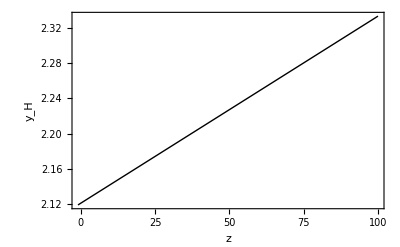

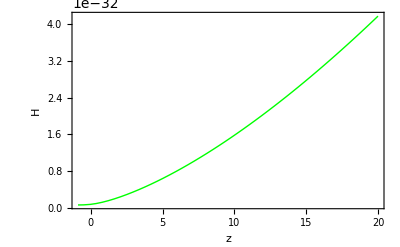

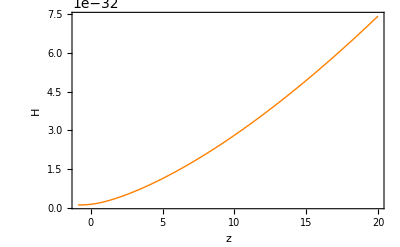

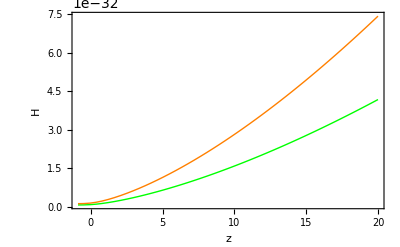

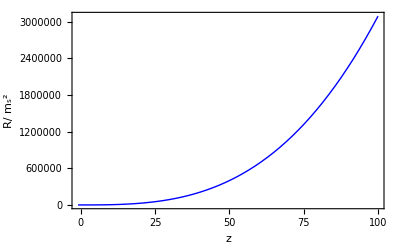

```mathematica
p1=Plot[yH[z],{z,-0.9,100},Frame->True,FrameLabel->{"z",Subscript["y","H"]},PlotRange->All,PlotStyle->Thick]
H1[z]=ms √(yH[z]+ρ[z]);
p2=Plot[H1[z],{z,-0.9,20},Frame->True,FrameLabel->{"z","H"},PlotRange->All,PlotStyle->{Green,Thick},PlotRange->All]
HΛCDM0=1.37187 10^-33;
ΩΛ=0.6847;
ΩM=0.3153-Ωr;
Ωr=8 10^-5;
HΛCDM[z]=HΛCDM0 √(ΩΛ+ΩM(1+z)^3+Ωr(1+z)^4);
p3=Plot[HΛCDM[z],{z,-0.9,20},Frame->True,FrameLabel->{"z","H"},PlotRange->All,PlotStyle->{Orange,Thick}]
Show[p2,p3]
R1[z]=12 H1[z]^2-6(1+z)D[H1[z],z]H1[z];
p4=Plot[R1[z]/ms^2,{z,-0.9,100},Frame->True,FrameLabel->{"z","R/"Superscript[Subscript["m","s"],2]},PlotRange->All,PlotStyle->{Blue,Thick}]
```

“

## 3. Statefinder Parameters.

To ascertain the validity of the model, we study the behaviour of 6 statefinder parameters and compare results directly with data. The analysis focuses mainly on the deceleration, jerk, snap, Om(z), EoS and Density parameter of Dark Energy, all of them rewritten as functions depending solely on redshift for the sake of consistency. Above each plot, the current model predicted value of the respective statefinder is presented.

-0.51894

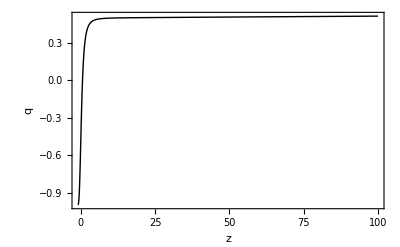

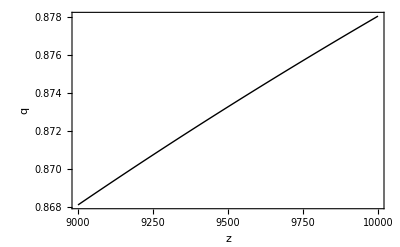

0.99952

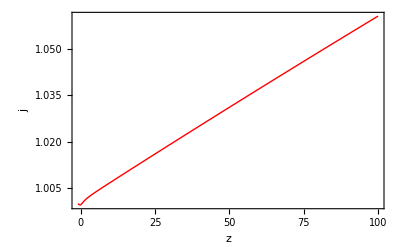

0.00015711

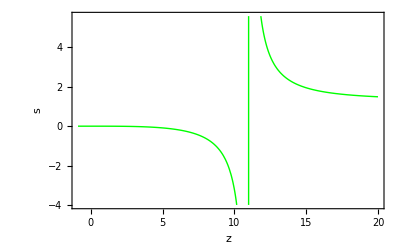

0.320707

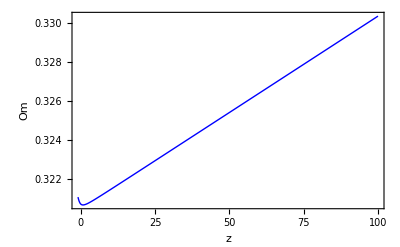

-0.999667

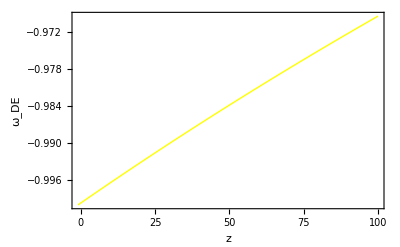

0.679553

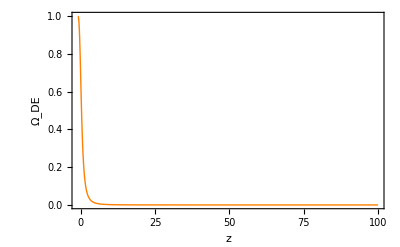

1.00026

```mathematica
q[z]=-1+(1+z)D[H1[z],z]/H1[z];
q[z]/.z->0//N
p5=Plot[q[z],{z,-0.9,100},Frame->True,FrameLabel->{"z","q"},PlotRange->All,PlotStyle->Thick]
p5b=Plot[q[z],{z,9000,10000},Frame->True,FrameLabel->{"z","q"},PlotRange->All,PlotStyle->Thick]
j[z]=(1+z)D[H1[z](1+z)D[H1[z],z],z]/H1[z]^2-3q[z]-2;
j[z]/.z->0//N
p6=Plot[j[z],{z,-0.9,100},Frame->True,FrameLabel->{"z","j"},PlotRange->All,PlotStyle->{Red,Thick}]
s[z]=(j[z]-1)/(3(q[z]-1/2));
s[z]/.z->0//N
p7=Plot[s[z],{z,-0.9,20},Frame->True,FrameLabel->{"z","s"},PlotStyle->{Green,Thick}]
H10=H1[z]/.z->0;
Om[z]=((H1[z]/H10)^2-1)/((1+z)^3-1);
Om0=Om[z]/.z->10^-8//N
p8=Plot[Om[z],{z,-0.9,100},Frame->True,FrameLabel->{"z","Om"},PlotRange->All,PlotStyle->{Blue,Thick}]
ωDE[z]=-1+(1+z)/(3yH[z])D[yH[z],z];
ωDE[z]/.z->0//N
p9=Plot[ωDE[z],{z,-0.9,100}, Frame->True,FrameLabel->{"z",Subscript["ω","DE"]},PlotRange->All,PlotStyle->{Yellow,Thick}]
ΩDE[z]=yH[z]/(yH[z]+ρ[z]);
ΩDE0=ΩDE[z]/.z->0//N
p10=Plot[ΩDE[z],{z,-0.9,100}, Frame->True,FrameLabel->{"z",Subscript["Ω","DE"]},PlotRange->All,PlotStyle->{Orange,Thick}]
Om0+ΩDE0
```

In general the fact that the snap diverges is expected as the deceleration parameter hits the value of q=0.5 that signifies the matter dominated era. It is expected from a viable numerical model as the jerk cannot be made to coincide mandatorily with unity, only approximately with deviations appearing in the third decimal.

## 4. Intensity Of Gravitational Waves.

In the final section we examine the significance of primordial gravitational waves. Assuming the existence of an f(R) gravity we find that for a dominantly negative value of aMdz gravitational waves can be indeed enhanced. For the effective EoS one observes that it remains relatively close to 0 however the higher the redshift the stronger the oscillation hence inevitably it deviates from such value.

Note: Adding a linear contribution in R does not affect the overall phenomenology, however the growth factor cannot be integrated properly, for some reason I obtain 0. I may need to change precision.

0.00303771

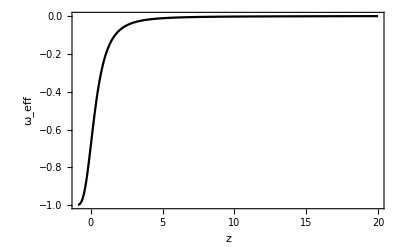

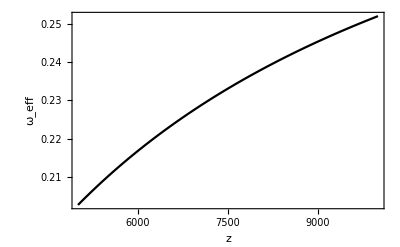

CheckMachineUnderflow→False

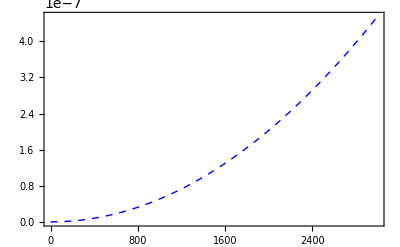

0.016797

```mathematica
weff[z]=-1+2/3(z+1)D[H1[z],z]/H1[z];
weff[z]/.z->29.42//N
Plot[Evaluate[weff[z]],{z,-0.9,20},Frame->True,FrameLabel->{"z",Subscript["ω","eff"]},PlotRange->All]
Plot[Evaluate[weff[z]],{z,5000,10000},Frame->True,FrameLabel->{"z",Subscript["ω","eff"]},PlotRange->All]
SetSystemOptions["CheckMachineUnderflow"->False]
aMdz=-D[f[R],{R,2}]/D[f[R],R]D[R1[z],z](z+1)/.R->R1[z]//Simplify;
Plot[Evaluate[aMdz/(1+z)],{z,-0.9,3000},Frame->True,PlotStyle->{Blue,Dashed,Thick}]
P=NIntegrate[aMdz/(1+z),{z,-0.9,10000},PrecisionGoal->10]
p11=Plot[Evaluate[-D[f[R],{R,2}]/D[f[R],R]/.R->R1[z]],{z,-0.9,3000},Frame->True,PlotStyle->{Thick,Red}];
p12=Plot[Evaluate[D[R1[z],z]],{z,-0.9,3000},Frame->True,PlotStyle->{Thick,Dashed,Blue}];
```

Here we see that the growth factor is positive therefore we can see dumping in the intensity due to the f(R) choice. So far it seems that it is rising so we expect an even larger value for the integral when redshift is increased.